```mathematica
(* Computer Graphics with Applications of Dr. Makhanov (Google's Version) *)
```

```mathematica
(* Lecture 2. 2D and 3D Graphics. Polar Plots. 2D Graphics primitives *)
```

```mathematica
SetOptions[{Plot,Plot3D,ParametricPlot,ParametricPlot3D,PolarPlot,Graphics},ImageSize->Medium];
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
(* We introduce 2 ways to define numerical functions  *)
```

```mathematica
(* 1) f1[arguments or list of arguments_]:={list of outputs} *)
```

```mathematica
(* Example 01. Explicit function f:R1->R1*)
```

```mathematica
f0[t_]:=Sin[t^2]+Log[t]
```

```mathematica
(* Call, graph: *)
```

```mathematica
f0[10.]
```

1.79622

```mathematica
(* The plot is saved in the variable Pexplicit0 *)
```

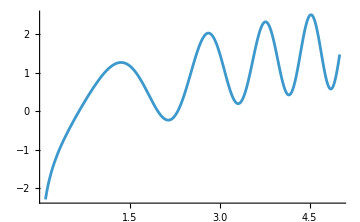

```mathematica
Pexplicit0=Plot[f0[t],{t,0.1,5}] (* ต้องเป็น 0.1 เพราะว่า log ไง log 0 is undefined แต่ว่าแม้ว่าจะใส่เป็น log0 Mathematica ก็ยังสามารถ plot ได้นะ *)
```

```mathematica
(* Example 02. Explicit function f:R2->R1 (surface in R3) *)
```

```mathematica
f1[x_,y_]:=Sin[x^2]+Log[x y^2]
```

```mathematica
(* Call, graph *)
```

```mathematica
f1[2.,2]
```

1.32264

```mathematica
Plot3D[f1[x,y],{x,0.1,5},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* Example 03 Parametric function f3:R1->R2 (curve in R2) *)
```

```mathematica
Clear[f3]
```

```mathematica
f3[t_]:={Sin[t^2]+Log[t^2+1],Cos[t]*t} (* Output for this function is a list *)
```

```mathematica
(* Call, graph: *)
```

```mathematica
f3[2.]
```

{0.852635,-0.832294}

```mathematica
(* ParametricPlot (this plot is saved in the variable Param3 for using later) *)
```

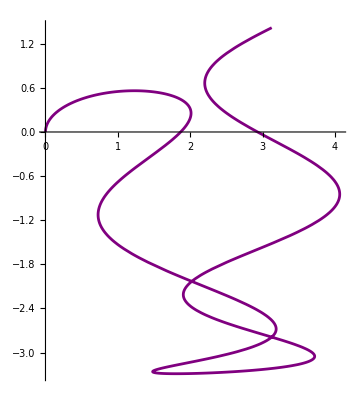

```mathematica
Param3=ParametricPlot[f3[t],{t,0,5},PlotStyle->Purple] (* For one x, you can have many value of y*)
```

```mathematica
(* 2) f[{input_list}_]:={output list}. A particular case is an explicit function f0L:R1->R1 *)
```

```mathematica
(* Example 0L f1L:Rn->R2. n>=2. Explicit function *)
```

```mathematica
f0L[a_]:=Sin[a[[1]]^2+Sin[a[[2]]^2]]
```

```mathematica
(* Call, graph: *)
```

```mathematica
f0L[{3.,4}] (* จริง ๆ ตรงนี้จะใส่ Input กี่ตัวก็ได้ แต่ว่าสุดท้ายมันก็จะถูก Ignore เพราะว่า function เอาแค่ 2 ตัวเลข— แต่ถ้ามี 1 argument จะไม่ work นะ555*)
```

0.653865

```mathematica
(* Symbolic *)
```

```mathematica
f0L[{a1,b1}] (* Haven't been defined colored in Blue *)
```

Sin[a1^2+Sin[b1^2]]

```mathematica
(* Graphics *)
```

```mathematica
Plot3D[f0L[{t,s}],{t,-1.5,1.5},{s,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[f0L[{banana,hippo}],{banana,-3,3},{hippo,-10,10}]
```

-Graphics3D-

```mathematica
(* Example 01. Parametric function in R2. f1L:Rn->R2, n>=1 *)
```

```mathematica
R:=1
```

```mathematica
f1L[a_]:={R Cos[a[[1]]],R/2 Sin[a[[1]]]} (* จริง ๆ a[[1]] เนี่ย เปลี่ยนเป็นแค่ a ก็ได้ *)
```

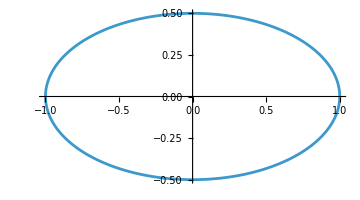

```mathematica
ParametricPlot[f1L[{t}],{t,0,2Pi}]
```

```mathematica
(* Example 02. Explicit function f1L:Rn->R1 in R2, n>=1 *)
```

```mathematica
f12L[a_]:=Sin[a[[1]]^2]+Log[a[[1]]^2] Sin[a[[2]]^2]
```

```mathematica
(* Check *)
```

```mathematica
f12L[{0.1,2}]
```

3.4952

```mathematica
(* Graph *)
```

```mathematica
Plot3D[f12L[{x,y}],{x,0.1,5},{y,0,3}]
```

-Graphics3D-

```mathematica
(*  Note: "pure" functions are introduced in L3 *)
```

```mathematica
(* Advanced *)
```

```mathematica
(* The general function converts any object to another object using rules. 
f[object1_]:=object2. Object denotes any allowed structure of M-14. In the example below the input and output are the plots  *)
```

```mathematica
f12P[x_,y_]:=Sin[x^2]+Log[x^2] Sin[y^2]
```

```mathematica
P1=Plot3D[f12P[x,y],{x,0.1,5},{y,0,3}]
```

-Graphics3D-

```mathematica
fany[P_]:=Show[P,BoxStyle->Directive[Dashed],AxesStyle->Directive[Red, Thick]]
```

```mathematica
(* Call with the variable P1 *)
```

```mathematica
fany[P1]
```

-Graphics3D-

```mathematica
(* Call with the variable P0 (Directive Box does not work here) *)
```

```mathematica
(* Polar Plots *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Examples *)
```

```mathematica
(* In the polar coordinates the function R=1 is a circle *)
```

```mathematica
R=1
```

1

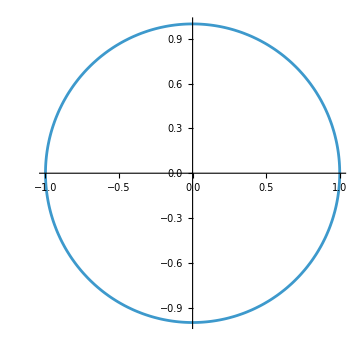

```mathematica
PolarPlot[R,{t,0,2Pi}]
```

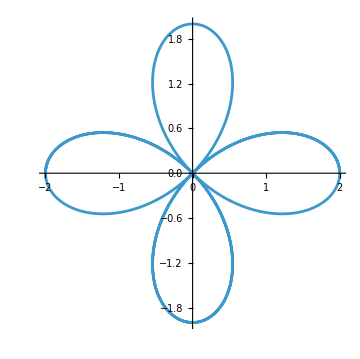

```mathematica
PolarPlot[2Cos[2t],{t,0,2Pi}] (* เพิ่มขึ้นมาเอง หา experiment เพิ่มเติมได้ *)
```

```mathematica
(* Some examples *)
```

```mathematica
(* Two Circles *)
```

```mathematica
R1=1
```

1

```mathematica
R2=2
```

2

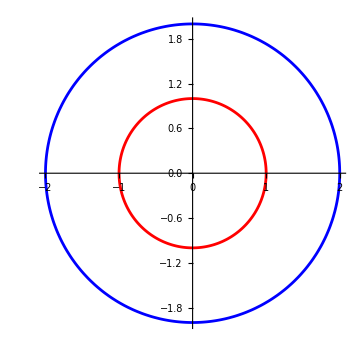

```mathematica
PolarPlot[{R1,R2},{t,0,2Pi},PlotStyle->{Red, Blue}] (* Several curve in PolarPlot *)
```

```mathematica
(* Include the polar function into the polar plot: R[t_]:=Sin[3t]   *)
```

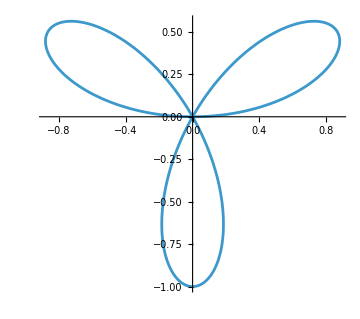

```mathematica
PolarPlot[Sin[3t],{t,0,Pi}]
```

```mathematica
(* Define the function "star"  *)
```

```mathematica
Clear[fR1]
```

```mathematica
fR1[t_]:=1+1/10 Sin[10t]
```

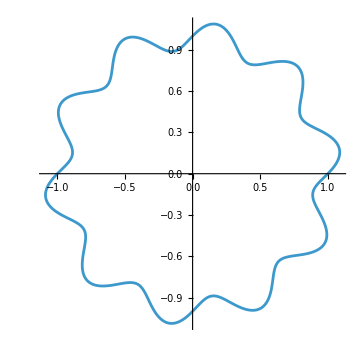

```mathematica
PolarPlot[fR1[t] ,{t,0,2Pi}]
```

```mathematica
(* Multiple polar plots -1 *)
```

```mathematica
fRn[t_,R_]:=R+1/10 Sin[10t]
```

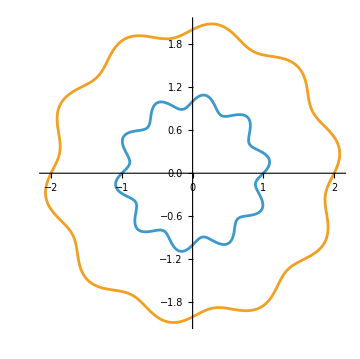

```mathematica
PolarPlot[{fRn[t,1],fRn[t,2]} ,{t,0,2Pi}] (* สมมติอยากได้วงกลมเพิ่มอีกกัน ก็แค่เพิ่ม , argument มาเลย*)
```

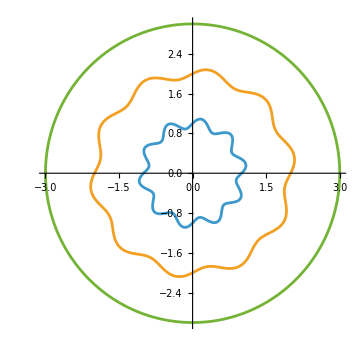

```mathematica
PolarPlot[{fRn[t,1],fRn[t,2], 3} ,{t,0,2Pi}] (* นี่ ๆ *)
```

```mathematica
(* Multiple polar plots -2 *)
```

```mathematica
fRk[t_,k_]:=1+1/k Sin[10t]
```

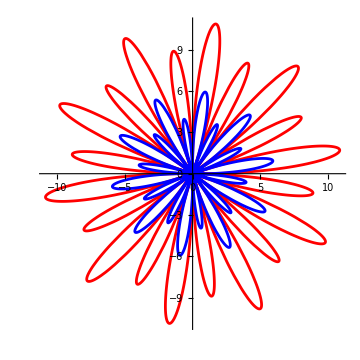

```mathematica
PolarPlot[{fRk[t,0.1],fRk[t,0.2]} ,{t,0,2Pi},PlotStyle->{Red,Blue}]
```

```mathematica
(* 3 polar plots combined *)
```

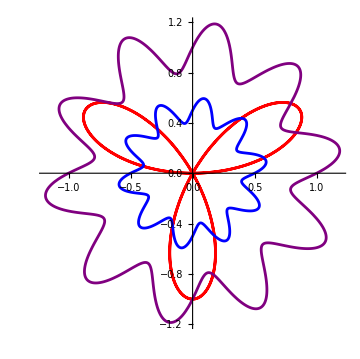

```mathematica
PolarPlot[{Sin[3t],fRn[t,0.5],fRk[t,5]},{t,0,2Pi},PlotStyle->{Red,Blue,Purple}]
```

```mathematica
(* Freeth’s Nephroid curve    *)
```

```mathematica
a=0.5
```

0.5

```mathematica
Nep[x_]:=a+2Sin[x/2]
```

```mathematica
(* "Star"- explicit function with the parameters in the polar coordinates *)
```

```mathematica
fRn[t_,R_]:=R+1/10 Sin[10t]
```

```mathematica
(* Combined plot *)
```

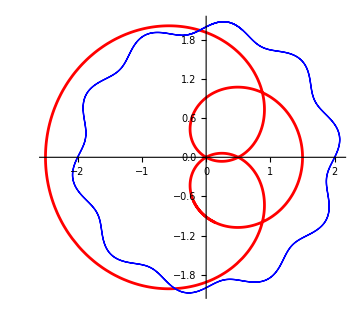

```mathematica
Ppolar1=PolarPlot[{Nep[t],fRn[t,2]},{t,-5,8},PlotStyle->{Red,{Blue,Thick}}]
```

```mathematica
(* The Hyperbolic Spiral  *)
```

```mathematica
aH=10
```

10

```mathematica
fH[t_]:=aH/t
```

```mathematica
(* The polar plot P2 is given by *)
```

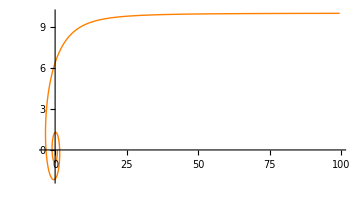

```mathematica
Ppolar2=PolarPlot[fH[t],{t,0.1,4Pi},PlotStyle->{Orange,Thick } ] (* เหมือนเคย จะใส่เป็น 0 เลยก็ได้ *)
```

```mathematica
(* Note that in Ppolar1 and Ppolar2 the independent var t changes in the different range. In this case  it is not possible to apply a single PolarPLot.  
Mathematica offers a function Show i.e. *)
```

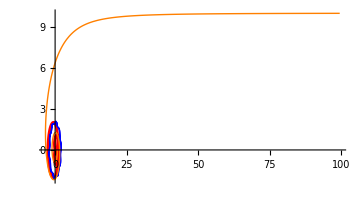

```mathematica
Show[{Ppolar1,Ppolar2}] (* อย่างข้างบนเรากำหนดให้ variable = PolarPlot เราก็สามารถใช้ Show มาโชว์แบบนี้ได้— ข้อดีก็คือ Plot type ไหนก็ได้ แต่คง 2d กับ 3d ไม่ได้นะ *)
```

```mathematica
(* Show superimposes plots with a different range or plots of a different type such as ParametricPlot, Plot  or Plot and PolarPlot *)
```

```mathematica
(* Combine the Parametric and the Polar plot using function "Show"  *)
```

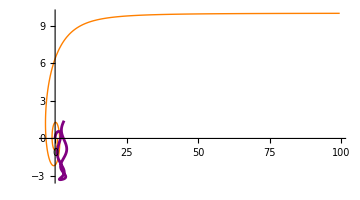

```mathematica
Show[Ppolar2,Param3]
```

```mathematica
(* This combines Parametric and Explicit plots  *)
```

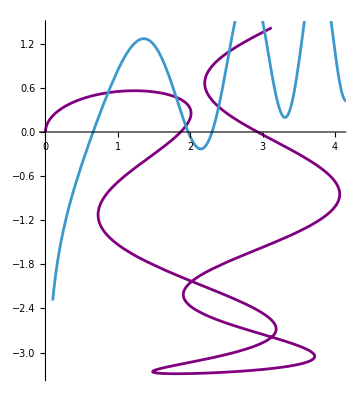

```mathematica
Show[{Param3,Pexplicit0}]
```

```mathematica
(* PlotRange must be fixed  *)
```

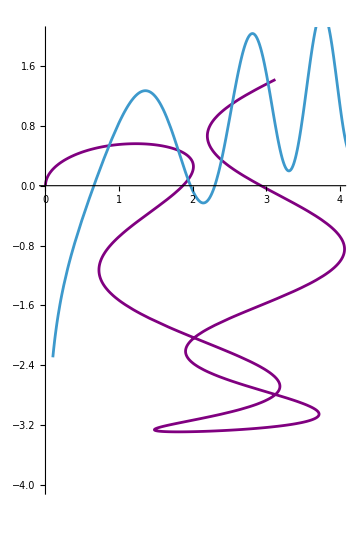

```mathematica
Show[{{Param3,Pexplicit0}},PlotRange->{{0,4},{-4,2}}] (* Show สามารถกำหนด Range ได้ด้วย อย่างเจ๋งอะ *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Define a Circle with the default value R=1 (Here, lecture 2 อาจารย์ยังไม่ explain)*)
```

```mathematica
CR1[t_,R_:1]:={R Cos[t],R Sin[t]}
```

```mathematica
CR1[Pi/2,5]
```

{0,5}

```mathematica
CR1[Pi/2]
```

{0,1}

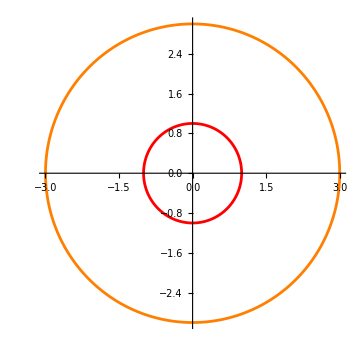

```mathematica
ParametricPlot[{CR1[t], CR1[t,3]},{t,0,2Pi},PlotStyle->{Red,Orange}]
```

```mathematica
(* Polar plot. Function with no arguments *)
```

```mathematica
CParamR1[R_:1]:=R
```

```mathematica
CParamR1[]
```

1

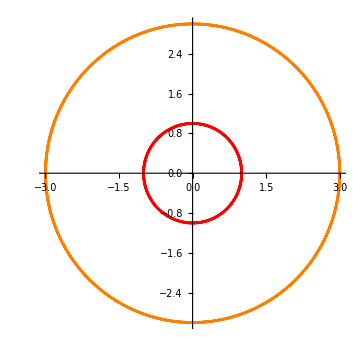

```mathematica
PolarPlot[{CParamR1[], CParamR1[3]},{t,0,4Pi},PlotStyle->{Red,Orange}]
```

```mathematica
(* 2D Primitives using the Wrapper Graphics เริ่มเรียนต่อตรงนี้ *)
```

```mathematica
(* พวกข้างล่างนี้ต้องการ wrapper เพื่อมาโชว์ให้เราเห็น ถ้ามีแค่ Point แบบนี้มันจะไม่โชว์ *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Plotting primitives *)
```

```mathematica
(* A single point  *)
```

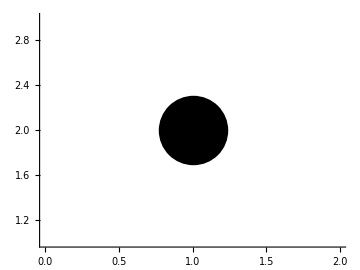

```mathematica
Graphics[{PointSize[0.15],Point[{1,2}]},PlotRange->3,Axes->True] (* PlotRange single value แบบนี้หมายถึง -3, 3 (ทั้ง x และ y) *)
```

```mathematica
(* Point size, color, axes. Pn1 a point with coordinates {1,2} *)
```

```mathematica
Pn1=Point[{1,2},VertexColors->Red]
```

Point[{1,2},VertexColors→RGBColor[1, 0, 0]]

```mathematica
(* Plot Pn1 *)
```

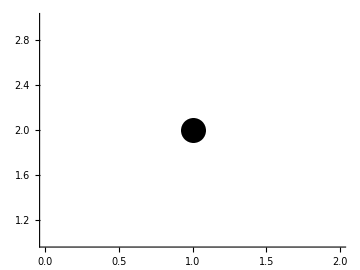

```mathematica
Graphics[{PointSize[0.05],Pn1}, Axes->True]
```

```mathematica
(* Multiple points, one color *)
```

```mathematica
Pn2={{1,2},{3,4},{2,-1}}
```

{{1,2},{3,4},{2,-1}}

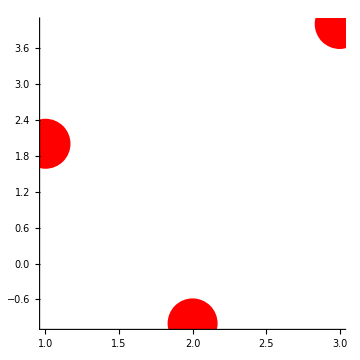

```mathematica
Graphics[{Red,PointSize[0.1],Point[Pn2]}, Axes->True,AspectRatio->1]
```

```mathematica
(* Different colors for different points *)
```

```mathematica
Col={Red,Blue,Orange}
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]}

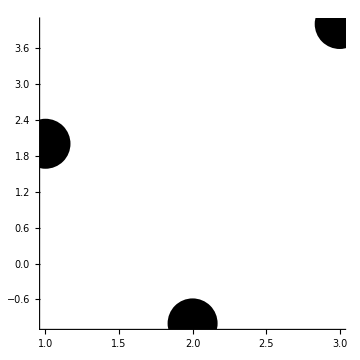

```mathematica
Graphics[{PointSize[0.1],Point[Pn2,VertexColors->Col]}, Axes->True,AspectRatio->1]
```

```mathematica
(* Example 2 Combine Plots of functions and primitives Using a wrapper
 Plot the spiral Spi[t_] (L1). Indicate the starting point (t=0) by red and the ending point (t=2 Pi by blue *)
```

```mathematica
RC[t_]:=R(2Pi-t)/(2Pi) (* Radius changing linearly*)
```

```mathematica
xt2[t_]:=RC[t]  Cos[t]
```

```mathematica
yt2[t_]:=RC[t] Sin[t]
```

```mathematica
Spi[t_]:={xt2[t],yt2[t]}
```

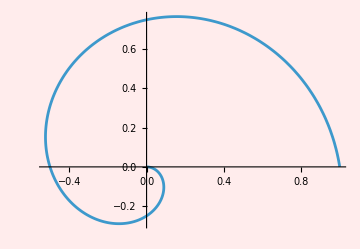

```mathematica
ParametricPlot[Spi[t],{t,0,2Pi},Background->LightPink]
```

```mathematica
(*Points PS (start) PE (end) displayed as primitives *)
```

```mathematica
PS=Spi[0]
```

{1,0}

```mathematica
PE=Spi[2 Pi]
```

{0,0}

```mathematica
(* Both points *)
```

```mathematica
PP={PS,PE}
```

{{1,0},{0,0}}

```mathematica
(* Primitives without the wrapper Graphics *)
```

```mathematica
PSEG={PointSize[0.1],Point[PP,VertexColors->{Red, Green}]}
```

{PointSize[0.1],Point[{{1,0},{0,0}},VertexColors→{RGBColor[1, 0, 0],RGBColor[0, 1, 0]}]}

```mathematica
(* Wrapper *)
```

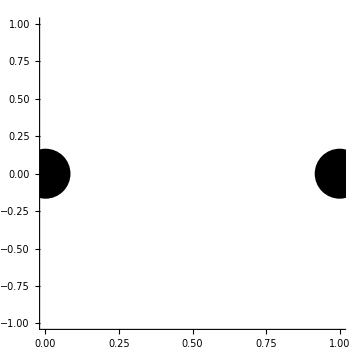

```mathematica
PSE=Graphics[PSEG,Axes->True,AspectRatio->1]
```

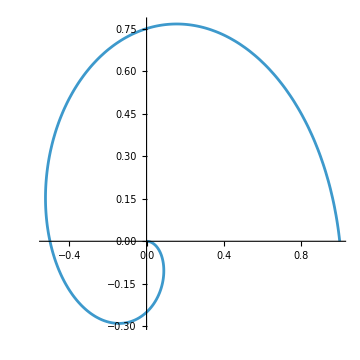

```mathematica
PSp1=ParametricPlot[Spi[t],{t,0,2 Pi}, Axes->True,AspectRatio->1]
```

```mathematica
(* Convert graphic objects into a collection of primitives (no wrapper) Important  *)
```

```mathematica
(* We will discuss here the structure of graphics objects represented by a list of primitives and options )
```

```mathematica
PSp1G=PSp1[[1]]; (* จริง ๆ มันก็เป็น List นั่นแหละ ลองเอา ; ออกสิ เห็นเลย *)
```

```mathematica
(* Wrapper for both primitives  *)
```

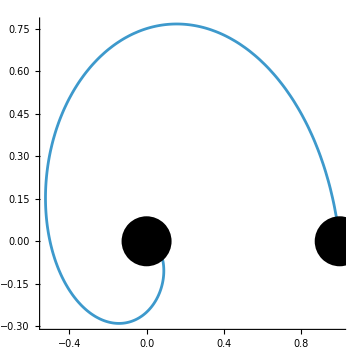

```mathematica
Graphics[{PSp1G,PSEG},Axes->True,AspectRatio->1]
```

```mathematica
(* Function "Array"*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 0 *)
```

```mathematica
Array[f, 10, {1, 10}] (* 10 ตัวแรกคือเอา 10 ตัว *)
```

{{1,Sin[1]},{2,Sin[4]},{3,Sin[9]},{4,Sin[16]},{5,Sin[25]},{6,Sin[36]},{7,Sin[49]},{8,Sin[64]},{9,Sin[81]},{10,Sin[100]}}

```mathematica
Clear[f]
```

```mathematica
Array[f, 10, {0,1.}]
```

{f[0.],f[0.111111],f[0.222222],f[0.333333],f[0.444444],f[0.555556],f[0.666667],f[0.777778],f[0.888889],f[1.]}

```mathematica
(* Create an array of 10 points {x,y} where x runs from 0 to 1 and y=Sin[x^2] *)
```

```mathematica
f[x_]:={x,Sin[x^2]}
```

```mathematica
P10=Array[f, 10, {0,1.}]
```

{{0.,0.},{0.111111,0.0123454},{0.222222,0.0493626},{0.333333,0.110883},{0.444444,0.196249},{0.555556,0.303765},{0.666667,0.429956},{0.777778,0.568711},{0.888889,0.71044},{1.,0.841471}}

```mathematica
(* RandomColor[] -returns a random RGB color *)
```

```mathematica
(* fPoint generates a single point or a collection of points P with the Random Colors *)
```

```mathematica
fPoint[P_]:=Point[P,VertexColors->RandomColor[]]
```

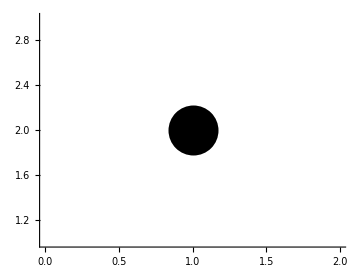

```mathematica
Graphics[{PointSize[0.1],fPoint[{1,2}]}, Axes -> True] (* ลองกดเล่นได้ Random Color จริง ๆ*)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 0 *)
```

```mathematica
Map[Sin,{0,Pi/4,3Pi/2}]
```

{0,1/(√2),-1}

```mathematica
(* Example 1 Two Random points with Random Colors  *)
```

```mathematica
P2=Map[fPoint,{{1,2},{5,6}}]
```

{Point[{1,2},VertexColors→RGBColor[0.7772171962703034, 0.37734486940275347, 0.18572735551748187]],Point[{5,6},VertexColors→RGBColor[0.7785952496482431, 0.7637189430972058, 0.05686391054579065]]}

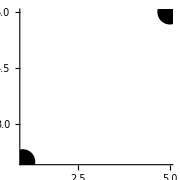

```mathematica
Graphics[{PointSize[0.1],P2},ImageSize->Small,Axes->True]
```

```mathematica
(* Apply fPoint to P10 *)
```

```mathematica
GP10=Map[fPoint,P10]
```

{Point[{0.,0.},VertexColors→RGBColor[0.7009525438530111, 0.49445846707617336, 0.3752912473210639]],Point[{0.111111,0.0123454},VertexColors→RGBColor[0.0017525739038311006, 0.9908349159835732, 0.2224953414925812]],Point[{0.222222,0.0493626},VertexColors→RGBColor[0.688566684420534, 0.20832443850002202, 0.533058665901861]],Point[{0.333333,0.110883},VertexColors→RGBColor[0.8642888706554059, 0.32204435049820956, 0.7323978096287425]],Point[{0.444444,0.196249},VertexColors→RGBColor[0.015003372635740808, 0.25263361848147725, 0.8149587939930598]],Point[{0.555556,0.303765},VertexColors→RGBColor[0.6765743773218837, 0.877609221752367, 0.818684508066591]],Point[{0.666667,0.429956},VertexColors→RGBColor[0.9893235086088226, 0.1992834976318525, 0.7103625695195332]],Point[{0.777778,0.568711},VertexColors→RGBColor[0.7701906175275202, 0.40949574390824717, 0.4385828593687766]],Point[{0.888889,0.71044},VertexColors→RGBColor[0.9050084812050614, 0.45052193651003436, 0.7656351838661675]],Point[{1.,0.841471},VertexColors→RGBColor[0.2225924176367975, 0.6208747089064195, 0.008642011392966387]]}

```mathematica
(* Plot points *)
```

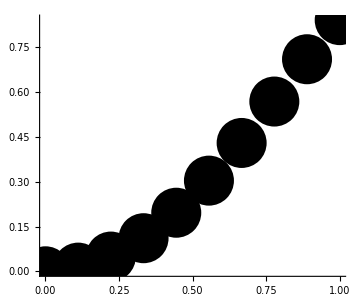

```mathematica
GPoints=Graphics[{PointSize[0.1],{GP10}}, Axes -> True]
```

```mathematica
(* Example 4 Recall that points and vectors represent the same mathematical entities. 
Let us depict points P10 as vectors using the function "Arrow"  *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Example 4.1 The basic arrow  *)
```

```mathematica
A0=Arrow[{{1,0},{4,1}}]
```

Arrow[{{1,0},{4,1}}]

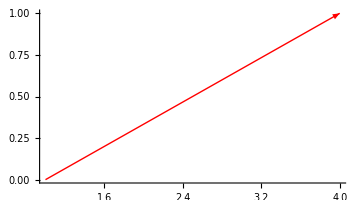

```mathematica
Graphics[{Red,A0}, Axes->True]
```

```mathematica
(* Example 4.1 Sequence of arrows  *)
```

```mathematica
A1=Arrow[{{1,0},{2,1},{3,0},{4,1}}]
```

Arrow[{{1,0},{2,1},{3,0},{4,1}}]

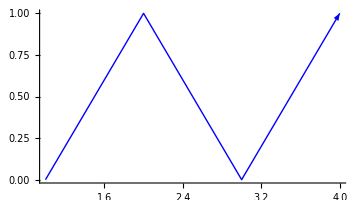

```mathematica
Graphics[{Blue,A1}, Axes->True]
```

```mathematica
(* Example 4.2 As apposed to 2 arrows (the same data is used)   *)
```

```mathematica
A2={Arrow[{{1,0},{2,1}}],Arrow[{{3,0},{4,1}}]}
```

{Arrow[{{1,0},{2,1}}],Arrow[{{3,0},{4,1}}]}

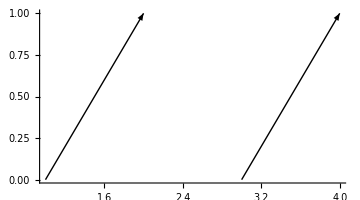

```mathematica
Graphics[A2, Axes->True]
```

```mathematica
(* A convert a point  into the vector *)
```

```mathematica
Clear[fCArrow]
```

```mathematica
(* Create an arrow from 0 to P} *)
```

```mathematica
fCArrow[P_]:=Arrow[{{0,0},P}]
```

```mathematica
(* Check *)
```

```mathematica
A3=Map[fCArrow,{{1,2},{5,6}}]
```

{Arrow[{{0,0},{1,2}}],Arrow[{{0,0},{5,6}}]}

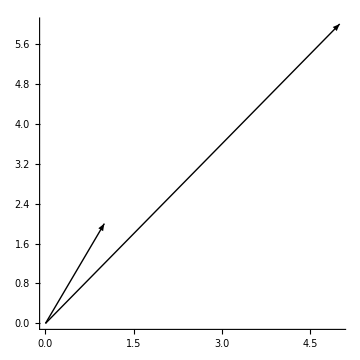

```mathematica
Graphics[{A3},Axes->True,AspectRatio->1]
```

```mathematica
(* Apply to P10 *)
```

```mathematica
Vectors1=Map[fCArrow,P10]
```

{Arrow[{{0,0},{0.,0.}}],Arrow[{{0,0},{0.111111,0.0123454}}],Arrow[{{0,0},{0.222222,0.0493626}}],Arrow[{{0,0},{0.333333,0.110883}}],Arrow[{{0,0},{0.444444,0.196249}}],Arrow[{{0,0},{0.555556,0.303765}}],Arrow[{{0,0},{0.666667,0.429956}}],Arrow[{{0,0},{0.777778,0.568711}}],Arrow[{{0,0},{0.888889,0.71044}}],Arrow[{{0,0},{1.,0.841471}}]}

```mathematica
(* Plot Vectors *)
```

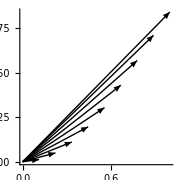

```mathematica
GArrows=Graphics[{Arrowheads[Medium],Vectors1},Axes->True,AspectRatio->1,ImageSize->Small]
```

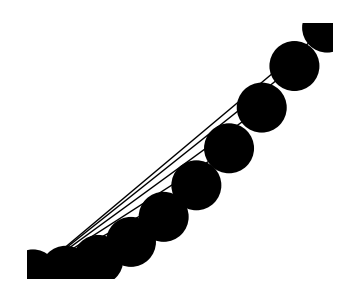

```mathematica
Show[GPoints,GArrows]
```

```mathematica
(* Example 5 Connects the points into a sequence of arrows/lines  *)
```

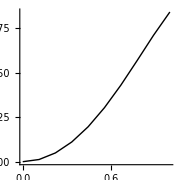

```mathematica
GLines=Graphics[Line[P10],ImageSize->Small,Axes->True]
```

```mathematica
(* Output *)
```

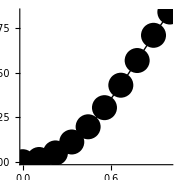

```mathematica
Show[{GLines,GPoints}]
```

```mathematica
(*  Self-study  Example 6 Sample the function f= {Sin[3 x], Sin[2 x]}  with the step Pi/10. Plot triangle around every sample point *)
```

```mathematica
Clear[fS]
```

```mathematica
fS[x_]:={Sin[3 x ], Sin[2 x]}
```

```mathematica
(* Visualize  *)
```

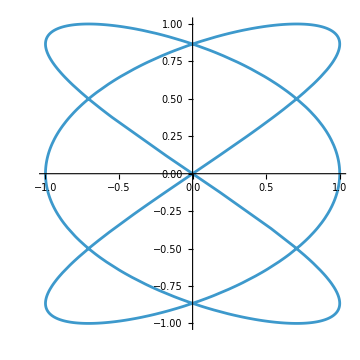

```mathematica
G0=ParametricPlot[fS[t],{t,0,2Pi}]
```

```mathematica
(* Change the variable for sampling from 0, to 19 (20 points)*)
```

```mathematica
n=40
```

40

```mathematica
30
```

30

```mathematica
Clear[fs1]
```

```mathematica
fs1[x_]:=fS[2Pi(x-1)/(n-1)]
```

```mathematica
(* Sample *)
```

```mathematica
Sf=1.0Array[fs1,n]
```

{{0.,0.},{0.464723,0.316668},{0.822984,0.600742},{0.992709,0.822984},{0.935016,0.960518},{0.663123,0.999189},{0.239316,0.935016},{-0.239316,0.774605},{-0.663123,0.534466},{-0.935016,0.239316},{-0.992709,-0.0804666},{-0.822984,-0.391967},{-0.464723,-0.663123},{0.,-0.866025},{0.464723,-0.979791},{0.822984,-0.992709},{0.992709,-0.90345},{0.935016,-0.721202},{0.663123,-0.464723},{0.239316,-0.160411},{-0.239316,0.160411},{-0.663123,0.464723},{-0.935016,0.721202},{-0.992709,0.90345},{-0.822984,0.992709},{-0.464723,0.979791},{0.,0.866025},{0.464723,0.663123},{0.822984,0.391967},{0.992709,0.0804666},{0.935016,-0.239316},{0.663123,-0.534466},{0.239316,-0.774605},{-0.239316,-0.935016},{-0.663123,-0.999189},{-0.935016,-0.960518},{-0.992709,-0.822984},{-0.822984,-0.600742},{-0.464723,-0.316668},{0.,0.}}

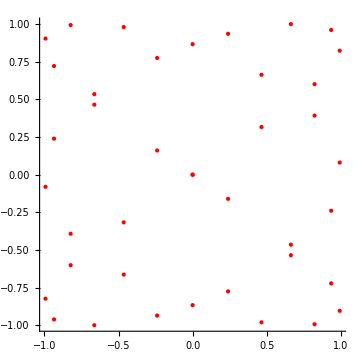

```mathematica
G1=Graphics[{Red,Point[Sf]},Axes->True]
```

```mathematica
(* In order to plot an equilateral triangle we use the functions CirclePoints and Polygon  *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
Tri=CirclePoints[0.1,3]
```

{{0.0866025,-0.05},{6.12323×10^-18,0.1},{-0.0866025,-0.05}}

```mathematica
(* Check using Polygon  *)
```

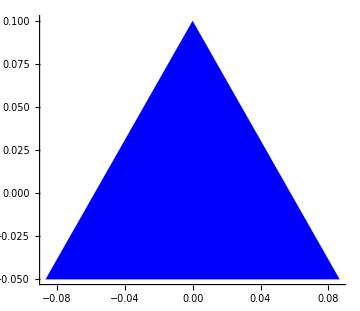

```mathematica
GTri=Graphics[{Blue,Polygon[Tri]},Axes->True,PlotRange->1]
```

```mathematica
(* Calculate coordinates of each triangle  *)
```

```mathematica
CT[i_]:={Tri[[1]]+Sf[[i]],Tri[[2]]+Sf[[i]],Tri[[3]]+Sf[[i]]}
```

```mathematica
CT[1]
```

{{0.0866025,-0.05},{6.12323×10^-18,0.1},{-0.0866025,-0.05}}

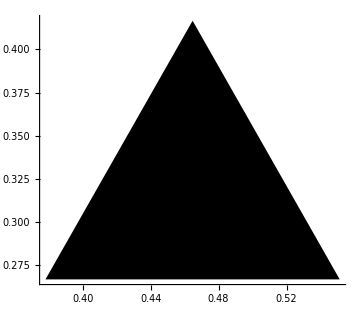

```mathematica
Graphics[Polygon[CT[2]],Axes->True,PlotRange->1]
```

```mathematica
P40=Polygon[Array[CT,n]]
```

Polygon[…]

```mathematica
P40
```

Polygon[…]

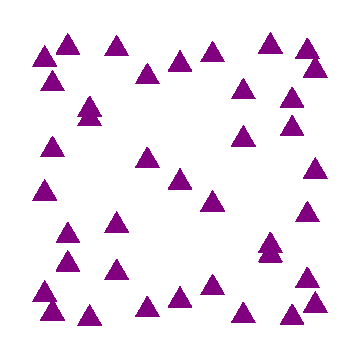

```mathematica
G2=Graphics[{Purple,P40}]
```

```mathematica
(* Check and compare *)
```

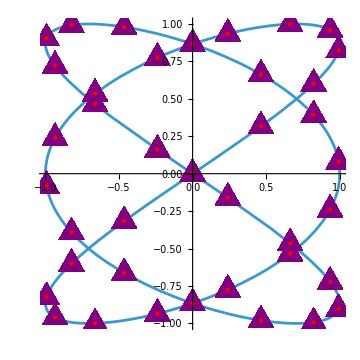

```mathematica
Show[G0,G2,G1]
```

```mathematica
(* Change the triangle to circle *)
```

```mathematica
CC[i_]:=Sf[[i]]
```

```mathematica
fC[i_]:=Circle[CC[i],0.1]
```

```mathematica
CCC=Array[fC,n];
```

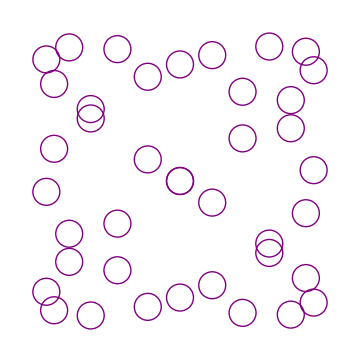

```mathematica
G4=Graphics[{Purple,CCC}]
```

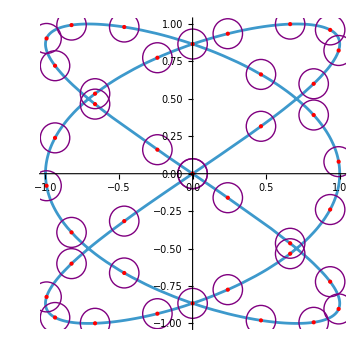

```mathematica
Show[G0,G1,G4]
```